# f.figure.rencon2.strange.baryons-all.interpolate.ci-1.5.nb

```mathematica
NotebookFileName[]
```

C:\octet.formfactor\f.figure.rencon2.strange.baryons-all.interpolate.ci-1.5.nb

使用插值的方法，处理图像数据，生成插值函数，然后重新画图，这样就可以研究每个图符号改变的影响了

## global setting

选定用来绘图的数据配置

```mathematica
fontsize`frame=8;
imagesize=Scaled[.6];
```

## data initial

## import origin figs

{Λ, ci}→

{0.8,1.0} l1c1,{0.9,1.0} l2c1,{1.0,1.0} l3c1,

{0.8,1.5} l1c2,{0.9,1.5} l2c2,{1.0,1.5} l3c2

```mathematica
directory`fig=FileNameJoin[{NotebookDirectory[],"/expression-fig/"}]
```

C:\octet.formfactor\expression-fig

```mathematica
fig`calc`baryons`ge`total`origin=
(
(Get[
FileNameJoin[{directory`fig,
#1
}
]
])&/@
{
(*+++++++++++++++++++++++++*)
"fig.separate.baryons.ge.tot.L-0.90.ci-1.5.m"
}
);
```

```mathematica
fig`calc`baryons`gm`total`origin=(
(Get[
FileNameJoin[{directory`fig,
#1
}
]
])&/@
{
(*+++++++++++++++++++++++++*)
"fig.separate.baryons.gm.tot.L-0.90.ci-1.5.m"
}
);
```

```mathematica
fig`calc`baryons`ge`total`origin//Dimensions
fig`calc`baryons`gm`total`origin//Dimensions
```

## test

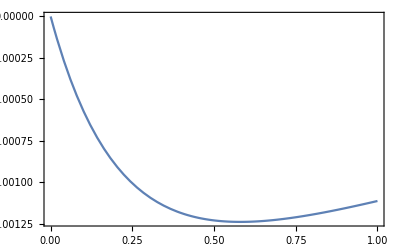

```mathematica
gegm=1;config=1;io=2;if=9;treeloop=2;
fig`calc`baryons`ge`total`origin⟦config,io,if,treeloop⟧
```

## import radius

导入半径信息

```mathematica
result`dir=FileNameJoin[{NotebookDirectory[],"/expression-results/"}]
```

C:\octet.formfactor\expression-results

```mathematica
Once[rearrange`radius2`gegm`seva=Get[FileNameJoin[{result`dir,
"rearrange`radius2`gegm`seva`gegm.total`L-0.90`ci-1.5.m"
}]]];
```

```mathematica
rearrange`radius2`gegm`seva//Dimensions
```

{2,9,8}

rearrange`radius2`gegm`seva,{2,9,8},{gegm,config,io}

(*1;"tree", all*)(*2;"tree", u*)(*3;"tree", d*)(*4;"tree", s*)
(*5;"loop", all*)(*6;"loop", u*)(*7;"loop", d*)(*8;"loop", s*)
(*9"all", all*)

```mathematica
gegm=1;seva=5;io=2;
rearrange`radius2`gegm`seva⟦gegm,seva,io⟧
```

{0.00317201,-0.0117852,0.000352439,0.00679937,0.00544497,-0.00660888,0.0264935,0.0024418,0.00172024,-0.0132353,-0.00504773}

## extract data

```mathematica
{data`f1[x_],data`f1[y_]}^:=data`f2[Join[x,y]]
```

```mathematica
{data`f1[x_]}^:=data`f2[x]
```

将Line中出现的数据用data`f1做tag，并且通过赋上值的方式合并到data`f2

f 是format的意思

fig`calc`baryons`ge`total`origin,{config,io,if,treeloop},{6,8,11,2}

```mathematica
fun`data`extract[fig`calc`baryons`ge`total`origin_]:=Table[
Cases[
fig`calc`baryons`ge`total`origin⟦config,io,if,treeloop⟧
,Line[x_]:>data`f1[x],10(*level*)
]
,{config,1,1,1}
,{io,1,8,1}
,{if,1,11,1}
,{treeloop,1,2,1}
]
```

```mathematica
data`calc`baryons`gegm`total={
fun`data`extract[fig`calc`baryons`ge`total`origin],
fun`data`extract[fig`calc`baryons`gm`total`origin]
};
```

```mathematica
data`calc`baryons`gegm`total//Dimensions
```

data`calc`baryons`gegm`total,{2,1,8,11,2}, {gegm,config,io,if,treeloop}

## interpolate

## interpolate functions

```mathematica
fun`interp`calc`baryons`gegm`total=Table[

data`calc`baryons`gegm`total⟦gegm,config,io,if,treeloop⟧/.data`f2->Interpolation

,{gegm,1,2,1}
,{config,1,1,1}
,{io,1,8,1}
,{if,1,11,1}
,{treeloop,1,2,1}
];
```

Interpolation::inddp: 维度 1 中的点 2.04082×10^-8 是重复的.

General::stop: 在本次计算中，Interpolation::inddp 的进一步输出将被抑制.

```mathematica
fun`interp`calc`baryons`gegm`total//Dimensions
```

{2,1,8,11,2}

## draw single

## style scheme

线型,Dashing[{}]指定线为实线

```mathematica
style`line`type={
(*1*)Dashing[{}],
(*2*)Dashing[Medium],
(*3*)Dashing[Medium],
(*4*)Dotted,
(*5*)Dotted,
(*6*)Dashing[{}],
(*7*)Dashing[Medium],
(*8*)Dashing[Medium],
(*9*)Dashing[Medium],
(*10*)Dotted,
(*11*)Dotted
};
```

给定颜色方案，

```mathematica
style`exp={
AbsoluteThickness[_]-> AbsoluteThickness[.8],
PointSize[_]->PointSize[0.02]
};
```

```mathematica
color`default = RGBColor[0.368417, 0.506779, 0.709798];
```

1,3,4,6;2,5,7,8

```mathematica
color`array={Red,Green,Blue,Black,Cyan,Magenta,Yellow};
```

```mathematica
style`colors`theme=Array[#&,11]
style`colors`theme⟦type⟧=color`array⟦Span[1,Length[type={1,6}]]⟧;
style`colors`theme⟦type⟧=color`array⟦Span[1,Length[type={2,3,7,8,9}]]⟧;
style`colors`theme⟦type⟧=color`array⟦Span[1,Length[type={4,5,10,11}]]⟧;
```

{1,2,3,4,5,6,7,8,9,10,11}

设定11幅图的曲线style

```mathematica
style`line=Table[
Directive[
style`line`thick,style`line`type⟦if⟧,style`colors`theme⟦if⟧,Opacity[1](*opacity of the curves*)
]
,{if,1,11,1}
];
```

## left boundarys

求出每个图的左边界

```mathematica
boundary`left`if=Table[
Min[(data`calc`baryons`gegm`total⟦gegm,config,io,if,treeloop⟧/.data`f2->Identity)⟦All,1⟧]
,{gegm,1,2,1}
,{config,1,1,1}
,{io,1,8,1}
,{if,1,11,1}
,{treeloop,1,2,1}
];
```

求出所有图左边界中的最大值

```mathematica
boundary`left=Table[
Max[boundary`left`if⟦gegm,config,io,All,treeloop⟧]
,{gegm,1,2,1}
,{config,1,1,1}
,{io,1,8,1}
,{treeloop,1,2,1}
];
```

```mathematica
boundary`left//Dimensions
```

{2,1,8,2}

## draw

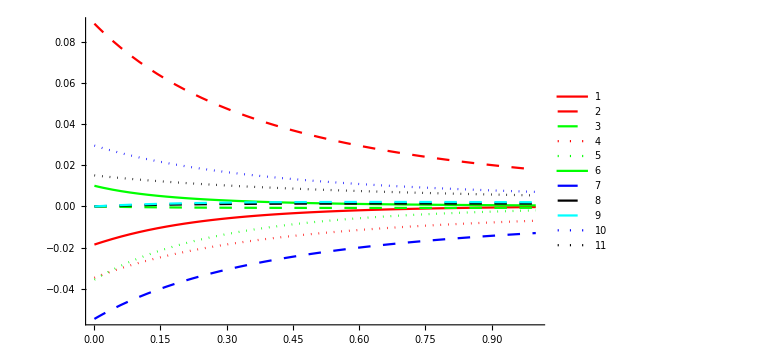

```mathematica
gegm=1;config=1;io=7;if=Span[1,11];treeloop=2;
tef=fun`interp`calc`baryons`gegm`total⟦gegm,config,io,if,treeloop⟧;
Plot[
Evaluate[
Through[tef[Q2]]
],
{Q2,boundary`left⟦gegm,config,io,treeloop⟧,1},
PlotRange->All,
ImageSize->Large,
PlotStyle->style`line,
PlotLegends->Range[Dimensions[tef]]
]
```

## presign and sum

## draw

改变每个图的符号，然后求和作图

```mathematica
pre`sign={
{(*+++++++++++++++++1*)
1,1,1(*3*),
1,(*4*)1,(*5*)
1,1,1,(*8*)1,(*9*)
1,1(*11*)
},
{(*+++++++++++++++++2*)
1,1,1(*3*),
1,(*4*)1,(*5*)
0,0,0,(*8*)0,(*9*)
0,0(*11*)
},
{(*+++++++++++++++++3*)
0,0,0(*3*),
0,(*4*)0,(*5*)
1,1,1,(*8*)1,(*9*)
1,1(*11*)
},
{(*+++++++++++++++++4*)
1,1,1(*3*),
1,(*4*)1,(*5*)
1,1,-1,(*8*)1,(*9*)
1,1(*11*)
},
{(*+++++++++++++++++5*)
1,1,1(*3*),
1,(*4*)1,(*5*)
1,1,1,(*8*)-1,(*9*)
1,1(*11*)
},
{(*+++++++++++++++++6*)
1,1,1(*3*),
1,(*4*)1,(*5*)
1,1,-1,(*8*)-1,(*9*)
1,1(*11*)
},
{(*+++++++++++++++++7*)
-1,-1,-1(*3*),
-1,(*4*)-1,(*5*)
1,1,1,(*8*)1,(*9*)
1,1(*11*)
},
{(*+++++++++++++++++8*)
1,1,1(*3*),
1,(*4*)1,(*5*)
-1,-1,-1,(*8*)-1,(*9*)
-1,-1(*11*)
}



};
```

gegm=1;config=1;io=2;if=Span[1,11];treeloop=2;

```mathematica
fun`draw[pre`sign_,fun`interp`calc`baryons`gegm`total_,gegm_,config_,io_,if_,treeloop_]:=CompoundExpression[
tef=fun`interp`calc`baryons`gegm`total⟦gegm,config,io,if,treeloop⟧,
te`left=boundary`left⟦gegm,config,io,treeloop⟧,
Plot[
Evaluate[
Total[
Through[tef[Q2]]*pre`sign
]
],
{Q2,te`left,1},
PlotRange->All,
ImageSize->Small,
PlotStyle->style`line,
PlotLegends->Range[Dimensions[tef]]
]
]
```

```mathematica
octet`name={"Σm","Σ0","Σp","pr","ne","Ξm","Ξ0","Λ"};
```

## draw test

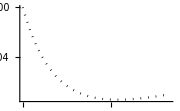
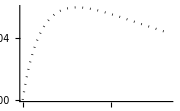
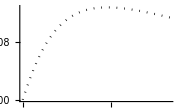
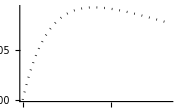
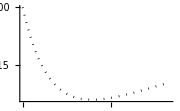
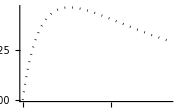
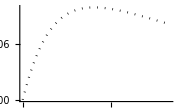
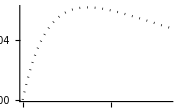
Σ0 | ne | Ξ0 | Λ
total | total | total | total
-Graphics- | -Graphics- | -Graphics- | -Graphics-
octet | octet | octet | octet
-Graphics- | -Graphics- | -Graphics- | -Graphics-
decuplet | decuplet | decuplet | decuplet
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[
Transpose[
{
{
gegm=1;config=1;io=2;if=Span[1,11];treeloop=2;
octet`name⟦io⟧,
(*+++++++++++++++++++++++++++++++++++*)
"total",
fun`draw[pre`sign⟦1⟧,fun`interp`calc`baryons`gegm`total,gegm,config,io,if,treeloop],
"octet",
fun`draw[pre`sign⟦2⟧,fun`interp`calc`baryons`gegm`total,gegm,config,io,if,treeloop],
"decuplet",
fun`draw[pre`sign⟦3⟧,fun`interp`calc`baryons`gegm`total,gegm,config,io,if,treeloop]
},
{
gegm=1;config=1;io=5;if=Span[1,11];treeloop=2;
octet`name⟦io⟧,
(*+++++++++++++++++++++++++++++++++++*)
"total",
fun`draw[pre`sign⟦1⟧,fun`interp`calc`baryons`gegm`total,gegm,config,io,if,treeloop],
"octet",
fun`draw[pre`sign⟦2⟧,fun`interp`calc`baryons`gegm`total,gegm,config,io,if,treeloop],
"decuplet",
fun`draw[pre`sign⟦3⟧,fun`interp`calc`baryons`gegm`total,gegm,config,io,if,treeloop]
},
{
gegm=1;config=1;io=7;if=Span[1,11];treeloop=2;
octet`name⟦io⟧,
(*+++++++++++++++++++++++++++++++++++*)
"total",
fun`draw[pre`sign⟦1⟧,fun`interp`calc`baryons`gegm`total,gegm,config,io,if,treeloop],
"octet",
fun`draw[pre`sign⟦2⟧,fun`interp`calc`baryons`gegm`total,gegm,config,io,if,treeloop],
"decuplet",
fun`draw[pre`sign⟦3⟧,fun`interp`calc`baryons`gegm`total,gegm,config,io,if,treeloop]
},
{
gegm=1;config=1;io=8;if=Span[1,11];treeloop=2;
octet`name⟦io⟧,
"total",
(*+++++++++++++++++++++++++++++++++++*)
fun`draw[pre`sign⟦1⟧,fun`interp`calc`baryons`gegm`total,gegm,config,io,if,treeloop],
"octet",
fun`draw[pre`sign⟦2⟧,fun`interp`calc`baryons`gegm`total,gegm,config,io,if,treeloop],
"decuplet",
fun`draw[pre`sign⟦3⟧,fun`interp`calc`baryons`gegm`total,gegm,config,io,if,treeloop]
}
}
]
]
```

## export

```mathematica
FileNameJoin[{directory`fig,"fun`interp`calc`baryons`gegm`total`L-0.90`ci-1.5.m"}]
```

C:\octet.formfactor\expression-fig\fun`interp`calc`baryons`gegm`total`L-0.90`ci-1.5.m

```mathematica
Export[
FileNameJoin[{directory`fig,"fun`interp`calc`baryons`gegm`total`L-0.90`ci-1.5.m"}],
fun`interp`calc`baryons`gegm`total
];
```